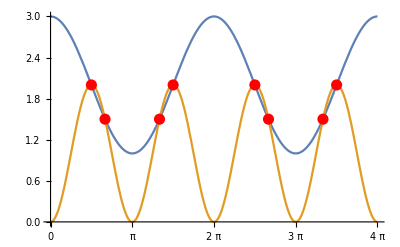

```mathematica
Plot[
{2 + Cos[x],2(Sin[x]^2)},
{x,0,4Pi},
Ticks->{Range[0,4Pi,Pi/2], Automatic},
Epilog->{
Red, PointSize[0.02],
Point[{#,2}]&/@{Pi/2,3Pi/2,5Pi/2,7Pi/2},
Point[{#,1.5}]&/@{2Pi/3,8Pi/3},
Point[{#,1.5}]&/@{4Pi/3,10Pi/3}
}
]
```

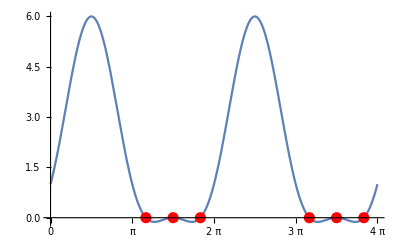

```mathematica
Plot[
2(Sin[x]^2)+3Sin[x]+1,
{x,0,4Pi},
Ticks->{Range[0,4Pi,Pi/2], Automatic},
Epilog->{
Red, PointSize[0.02],
Point[{#,0}]&/@{3Pi/2,7Pi/2},
Point[{#,0}]&/@{7Pi/6,19Pi/6},
Point[{#,0}]&/@{11Pi/6,23Pi/6}
}
]
```

```mathematica
Manipulate[
Row[
{
Plot[
Cos[x],
{x,-1.75,1.75},
ImageSize->Medium,
Ticks->{Range[-Pi/2,Pi/2,Pi],{0,1}},
PlotRange->{{-2,2},{-.2,1.2}},
PlotStyle->Black,
AxesStyle->Black,
Prolog->{
Red,EdgeForm[{Black}],Rectangle[{-z,0},{z,Cos[z]}]
}
],

Plot[
2 x(Cos[x]),
{x,0,Pi/2},
ImageSize->Medium,
PlotStyle->Black,
AxesStyle->Black,
Axes->True,
Ticks->{Range[0,Pi/2,Pi/6],{0,1}},
PlotRange->{{-.2,Pi/2},{-.2,1.2}},
Epilog->{
Red,PointSize[0.02],Point[{z,2 z(Cos[z])}]
}
]

}],
{{z,0.860334},0,Pi/2}
]
```